# Mathematica Bootcamp: Step 4

전경원 박사

Machine Learning Research Engineer
(주)시정
ruddyscent@gmail.com

2021년 10월 18일 월요일

## Access to Lecture Materials

최신 자료는 아래 링크에서 내려받으실 수 있습니다.

https://github.com/ruddyscent/mathematica-bootcamp-2021

## References

체험하며 배우는 WOLFRAM MATHEMATICA
-Graphics-

Wolfram 언어 기초 입문
-Graphics-

Hands-on Start to Mathematica Online, Wolfram U
https://www.wolfram.com/wolfram-u/hands-on-start-to-mathematica-online/

## Calculus

## Differentiation

전미분: Dt

```mathematica
Dt[a x^2 Sin[x],x]
```

TraditionalForm@HoldForm@Dt[a x^2 Sin[x],x]==Dt[a x^2 Sin[x],x]

편미분: D

```mathematica
D[a x^2 Sin[x],x]
```

HoldForm@D[a x^2 Sin[x],x]==D[a x^2 Sin[x],x]//TraditionalForm

고계 도함수

```mathematica
D[a x^2 Sin[x],{x,3}]
```

다변수 함수

∂/(∂y)∂/(∂x)(x^2 Cos[xy]+y^2 Sin[xy])

D[x^2 Cos[x y]+y^2 Sin[x y],x,y]

임의 함수 미분

```mathematica
D[g[x^2]g''[x],x]
```

D[g[x^2]g''[x],x]
%/.g→Sin

수식 정리

```mathematica
D[Sin[x]^10,{x,4}]
```

D[Sin[x]^10,{x,4}]
%//Simplify

## f(x)=x^3-2 x^2-4x+6의 도함수

도함수를 구하려면,

{f[x],f'[x],f''[x]}

{f[x],f'[x],f''[x]}
%/.f→(#^3-2#^2-4#+6&)

도함수의 그래프를 그리려면,

{f[x],f'[x],f''[x]}
%/.f→(#^3-2#^2-4#+6&)
Plot[%,{x,-3,3}]

{f[x],f'[x],f''[x]}
%/.f→(#^3-2#^2-4#+6&)
Plot[%,{x,-3,3},PlotLegends→{f[x],f'[x],f''[x]}]

도함수의 값을 표로 구하려면,

Table[{x,6-4 x-2 x^2+x^3,-4-4 x+3 x^2,-4+6 x},{x,-3,3}]//TableForm

## Limit

x가 1로 접글할 때, 1/x의 값을 구하려면,

```mathematica
Limit[1/x,x->1]
```

HoldForm@Limit[1/x,x→1]==Limit[1/x,x→1]

x가 무한히 커질 때, 1/x의 값을 구하려면,

```mathematica
Limit[1/x,x->Infinity]
```

```mathematica
Limit[1/x,x->∞]
```

좌극한, 우극한

```mathematica
Plot[1/x,{x,-3,3}]
```

Limit[1/x,x→0,Direction→1]

Limit[1/x,x→0,Direction→-1]

Limit[1/x,x→0]

When Limit cannot compute a limit,

```mathematica
Limit[x^a,a->∞]
```

Limit[x^a,a→∞,Assumptions→Log[x]>0]

Limit[x^a,a→∞,Assumptions→x>1]

Limit[x^a,a→∞,Assumptions→x==1]

Limit[x^a,a→∞,Assumptions→0≤x<1]

## Indefinite Integration

```mathematica
Integrate[x^2+x+1,x]
```

∫(x^2+2x+1)ⅆx

Integrate[x^2+x+1,x,GeneratedParameters→C]

## Definite Integration

```mathematica
Integrate[x^2 ⅇ^x,{x,0,1}]
```

-2+ⅇ

```mathematica
Integrate[x^2 ⅇ^x,{x,a,b}]
%/.{a->0,b->1}
```

-((2+(-2+a) a) ⅇ^a)+(2+(-2+b) b) ⅇ^b

-2+ⅇ

```mathematica
HoldForm@∫_a^b x^2 ⅇ^x ⅆx==∫_a^b x^2 ⅇ^x ⅆx
```

∫_a^b x^2 ⅇ^xⅆx==-((2+(-2+a) a) ⅇ^a)+(2+(-2+b) b) ⅇ^b

## Manipulate

```mathematica
Integrate[x^2 ⅇ^x,{x,0,a}]
```

-2+(2+(-2+a) a) ⅇ^a

```mathematica
Manipulate[Integrate[x^2 ⅇ^x,{x,0,a}],{a,0,8}]
```

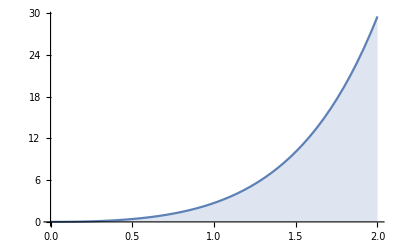

```mathematica
Plot[x^2 ⅇ^x,{x,0,2},Filling->Axis]
```

Manipulate[Plot[x^2 ⅇ^x,{x,0,a},Filling→Axis],{a,0.1,8}]

Manipulate[Plot[x^2 ⅇ^x,{x,0,a},Filling→Axis,PlotLabel→"색칠한 부분의 면적은 "<>ToString[Integrate[x^2 ⅇ^x,{x,0,a}]]<>"입니다."],{a,0.1,8}]

## Wolfram Demonstration Project

https://demonstrations.wolfram.com

## Multiple Integrals

```mathematica
Integrate[x^3 Sin[y]+y^2 Cos[x^2],{x,-1,1},{y,-2,x}]
```

8/3 √(2 π) FresnelC[√(2/π)]

```mathematica
∫_-1^1 ∫_-2^x f[x,y]ⅆyⅆx
%//FullForm
```

∫_-1^1 ∫_-2^x f[x,y]ⅆyⅆx

Integrate[f[x,y],List[x,-1,1],List[y,-2,x]]